# Tarea 3:

Este es un notebook hecho por Junior Zambrano para la tercera tarea del curso FS-2211 (Física 3) dictado por el profesor Sttiwuer Díaz.

En esta primera parte del código se limpian todas las variables de entorno y se definen las funciones de Ley de Coulomb para calcular la fuerza eléctrica y de campo eléctrico. Para correr todo el notebook y así poder cargar en memoria las funciones y variables correctamente seguir las siguientes instrucciones:

Ir a la sección “Evaluation” de la barra de herramientas.

Correr “Evaluate notebook”.

A continuación, una descripción de las funciones definidas en cuestión (créditos a Sttiwuer Díaz):
⌘ Función para la fuerza eléctrica sobre la carga q_i debido a la carga q_j ⟶ F_e[q_f,(r⃗)_f,q_i,(r⃗)_i], donde (r⃗)_i y (r⃗)_j son las posiciones de las carga q_i y q_j, respectivamente.
⌘ Función para el campo eléctrico en el punto P debido a la carga q_i ⟶ E_e[(r⃗)_p,q,(r⃗)_q], donde (r⃗)_p y (r⃗)_q son las posiciones del punto P y de la carga q, respectivamente.

```mathematica
Clear["Global`*"]
Fe[qf_,rf_,qi_,ri_]:=Subscript[K, 0](qf qi)/Norm[rf-ri]^3(rf-ri)//FullSimplify;
Ee[rp_,q_,rq_]:=Subscript[K, 0] q/Norm[rp-rq]^3(rp-rq)//FullSimplify;
```

##### Planteamiento A:

-Graphics-

En la figura adjunta se muestra un triángulo equilátero de lado L  y en los vértices del triángulo se han dispuestos tres cargas negativas iguales de valor -q; donde q es una constante positiva con dimensiones de carga. En el baricentro del triángulo se dispone una carga positiva de valor q. Sobre la base de este planteamiento responda las siguientes preguntas:

(1a) La fuerza eléctrica sobre la carga ubicada en el punto A, debido a las cargas restantes.

Ponemos el origen del sistema de coordenadas en la carga negativa ubicada en el vértice izquierdo (será el mismo para el resto del ejercicio) y hallamos la posición de la carga positiva respecto a este sistema que, por estar en el baricentro del triángulo, no es trivial:

```mathematica
Ba={(L+0+L/2)/3,(0+0+(√3)/2 L)/3}
```

{L/2,L/(2 √3)}

Definimos la posición del punto A:

```mathematica
A = {L/2,(√3)/2 L}
```

{L/2,(√3 L)/2}

Calculamos la fuerza eléctrica total sobre la carga negativa en el punto A usando el principio de superposición de fuerzas:

```mathematica
Refine[Fe[-q,A,-q,{0,0}]+Fe[-q,A,-q,{L,0}]+Fe[-q,A,q,Ba],L>0]// FullSimplify
```

{0,((-3+√3) q^2 K_0)/L^2}

(1b) Si se coloca una cuarta carga de valor -2q en el punto medio entre las carga ubicada en la base del triángulo equilátero, determine la fuerza eléctrica sobre dicha carga debido a las cargas restantes.

Definimos el valor y la posición de la quinta carga:

```mathematica
q5=-2q
```

-2 q

```mathematica
r5={L/2,0}
```

{L/2,0}

Calculamos la fuerza total sobre esta quinta carga usando el principio de superposición de fuerzas:

```mathematica
Refine[Fe[q5,r5,-q,{0,0}]+Fe[q5,r5,-q,{L,0}]+Fe[q5,r5,q,Ba]+Fe[q5,r5,-q,A],L>0]//FullSimplify
```

{0,(64 q^2 K_0)/(3 L^2)}

(1c) El campo eléctrico en el punto medio entre las dos carga negativas que se encuentran en la arista derecha del triángulo, debido al conjunto de cuatro cargas.

Definimos la posición del punto:

```mathematica
P={(L/2+L)/2,(0+(√3)/2 L)/2}
```

{(3 L)/4,(√3 L)/4}

Calculamos el campo eléctrico total usando el principio de superposición de campos eléctricos:

```mathematica
Refine[Ee[P,-q,{0,0}]+Ee[P,-q,{L,0}]+Ee[P,q,Ba]+Ee[P,-q,A],L>0]//FullSimplify
```

{(16 q K_0)/(√3 L^2),(16 q K_0)/(3 L^2)}

##### Planteamiento B:

-Graphics-

En la figura adjunta se muestra un semi-aro de radio R y con una carga positiva Q distribuida uniformemente en toda su longitud. Considere que un elemento infinitesimal de carga dq se encuentra localizado en un ángulo θ, dicho ángulo es medido respecto a la vertical tal como se indica en la figura adjunta. También considere que la longitud de arco s sobre el alambre es medido respecto al eje vertical, tal como se indica. En el origen del sistema de coordenadas se encuentra un carga puntual Q. Sobre la base de este planteamiento responda las siguientes preguntas:

(2a) La fuerza eléctrica que ejerce el semi-aro sobre la carga ubicada en el origen.

Calculamos la fuerza eléctrica que ejerce la distribución de carga continua sobre la carga Q. Ponemos el centro del sistema de coordenadas en la posición de Q y, en base a los datos presentados por la imagen del problema, definimos la posición del diferencial de carga dq parametrizando la curva del semi-aro:

```mathematica
Refine[Fe[Subscript[Q, 0],{0,0},dq,{R Sin[θ],R Cos[θ]}],{R>0,0≤θ≤π/2}]//FullSimplify
```

{-(dq Sin[θ] K_0 Q_0)/R^2,-(dq Cos[θ] K_0 Q_0)/R^2}

```mathematica
FQ={-(Q Sin[θ] Subscript[K, 0] Subscript[Q, 0])/(π R^2),-(Q Cos[θ] Subscript[K, 0] Subscript[Q, 0])/(π R^2)}
```

{-(Q Sin[θ] K_0 Q_0)/(π R^2),-(Q Cos[θ] K_0 Q_0)/(π R^2)}

Definimos al diferencial de carga dq, teniendo en cuenta que dq=λ_s ds y que ds=Rdθ, de modo que dq=λ_s Rdθ:

```mathematica
dq=Q/π
```

Q/π

Finalmente, integramos la fuerza obtenida respecto al diferencial de ángulo dθ:

```mathematica
Integrate[FQ,{θ,-π/2,π/2}]//FullSimplify
```

{0,-(2 Q K_0 Q_0)/(π R^2)}

(2b) Compare la fuerza calculada en el inciso anterior con la fuerza eléctrica que ejerce el semi-aro si toda su carga está concentrada en el centro de masa del aro. Suponga que la masa del semi-aro se distribuye de igual manera que la carga.

Calculamos la posición del centro de masa del semi-aro, teniendo en cuenta que su diferencial de masa es dm=M/π dθ:

```mathematica
rcm=Integrate[{R Sin[θ],R Cos[θ]}/M M/π,{θ,-π/2,π/2}]//FullSimplify
```

{0,(2 R)/π}

Calculamos la fuerza eléctrica sobre la carga Q_0 mediante la Ley de Coulomb:

```mathematica
Refine[Fe[Subscript[Q, 0],{0,0},Q,rcm],R>0]//FullSimplify
```

{0,-(π^2 Q K_0 Q_0)/(4 R^2)}

##### Planteamiento C:

-Graphics-

En una taza de cerámica posee en su interior una forma de arco de elipse, cuya ecuación queda descrita por 4 x^2+9 y^2=36 b^2. Dos cuerpos de igual masa m y carga q, se encuentran a la misma profundidad en el interior de la taza y separados entre si por una distancia igual al p% de la longitud del eje mayor 2ℓ, donde ℓ es la semi-longitud del eje mayor que se debe determinar. Suponga que las cargas se encuentran en reposo y están bajo la acción del campo gravitacional terrestre, tal como se ilustra en la figura adjunta. Sobre la base de este planteamiento responda las siguientes preguntas:

(3a) Encuentre el valor de la carga eléctrica en términos de los parámetros m, g, b y el parámetro p.

Identificamos la longitud del semi-eje mayor (el horizontal, en este caso) igualando a uno la ecuación de la elipse dada y observando la raíz cuadrada del denominador de la variable x:

```mathematica
ℓ=3b
```

3 b

Definimos la posición de la carga izquierda y derecha, respectivamente. Denotaremos por h a la componente y de la posición de las cargas, como podrá notarse más adelante el valor de esta cantidad no importará realmente en el cálculo que haremos:

```mathematica
rqi={-p ℓ,h}
rqd={p ℓ,h}
```

{-3 b p,h}

{3 b p,h}

Ahora, de la ecuación de fuerzas de los ejes x e y que actúan sobre la partícula izquierda queremos calcular la magnitud de la fuerza eléctrica que actúa sobre dicha partícula:

```mathematica
Solve[-Subscript[F, e]+n Cos[θ]==0,n]
```

{{n→Sec[θ] F_e}}

```mathematica
Solve[-m g +n Sin[θ]==0,n]
```

{{n→g m Csc[θ]}}

```mathematica
Solve[Sec[θ] Subscript[F, e]==g m Csc[θ],Subscript[F, e]]
```

{{F_e→g m Cot[θ]}}

Calculamos la fuerza eléctrica que ejerce la partícula derecha sobre la izquierda usando la Ley de Coulomb y luego la igualamos con la magnitud que acabamos de hallar, de modo que:

```mathematica
Solve[Refine[Norm[Fe[q,rqi,q,rqd]],{q>0,b>0,p>0,Subscript[K, 0]>0}]==g m Cot[θ],q]//FullSimplify
```

{{q→-(6 b √g √m p √Cot[θ])/(√K_0)},{q→(6 b √g √m p √Cot[θ])/(√K_0)}}

Como ambas partículas experimentan una interacción del tipo repulsiva, entonces no importa el signo que escojamos de esta siempre que dicha carga para ambas partículas tenga la misma magnitud y mismo signo.

Para hallar el valor de la Tan[θ], despejamos y de la ecuación de la elipse y derivamos respecto a x para obtener la pendiente de la recta tangente en cada punto de la elipse. Como estamos trabajando con la semi-elipse inferior, entonces nos quedaremos con el valor negativo de y:

```mathematica
Solve[4 x^2+9 y^2==36 b^2,y]//FullSimplify
```

{{y→-2/3 √(9 b^2-x^2)},{y→2/3 √(9 b^2-x^2)}}

```mathematica
D[-2/3 √(9 b^2-x^2),x]
```

(2 x)/(3 √(9 b^2-x^2))

Invertimos este valor y multiplicamos por -1 para obtener la pendiente de la recta normal a la recta tangente para cada punto de la elipse y luego sustituimos el valor de x por la posición x de la partícula izquierda:

```mathematica
Refine[-(3 √(9 b^2-x^2))/(2 x)/.x->-p ℓ//FullSimplify,{b>0,p>0}]
```

(3 √(1-p^2))/(2 p)

(3 √(1-p^2))/(2 p)

(3 √(1-p^2))/(2 p)

«1 more identical outputs»

Para comprobar el resultado que acabamos de obtener, construiremos una elipse de b=1∧p=0.5 e incluiremos las rectas tangente y normal en una hipotética partícula izquierda :

```mathematica
xp=-p ℓ/.{b->1,p->0.5};
yp=el/.x->-p ℓ/.{b->1,p->0.5};
pt=(2 x)/(3 √(9 b^2-x^2))/.{x->xp,b->1}
pn=(3 √(1-p^2))/(2 p)/.p->0.5
el=-2/3 √(9 b^2-x^2)/.b->1
rt=pt(x-xp)+yp
rn=pn(x-xp)+yp
```

-0.3849

2.59808

-2/3 √(9-x^2)

-1.73205-0.3849 (1.5+x)

-1.73205+2.59808 (1.5+x)

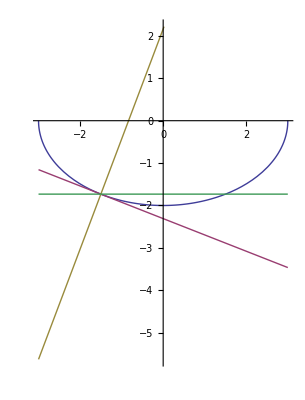

```mathematica
Plot[{el,rt,rn,yp},{x,-3,3},AspectRatio->Automatic]
```

Finalmente, sustituimos el valor que obtuvimos en la ecuación de la carga y declaramos una variable que contenga las condiciones que utilizaremos para las cantidades conocidas a partir de ahora:

```mathematica
Cond={g>0,m>0,q>0,b>0,1>p>0,Subscript[K, 0]>0};
```

```mathematica
FullSimplify[(6 b √g √m p √Cot[θ])/(√Subscript[K, 0])/.Cot[θ]->(2p)/(3 √(1-p^2)),Cond]
```

2 √6 b p √((g m p)/(√(1-p^2) K_0))

(b) El valor de la intensidad de la fuerza normal, que le ejerce la taza de cerámica a cada carga eléctrica.

Calculamos el valor de la intensidad de la fuerza eléctrica sustituyendo el valor de la carga que acabamos de obtener en la Ley de Coulomb que ya trabajamos:

```mathematica
qp=2 √6 b p √((g m p)/(√(1-p^2) Subscript[K, 0]))
```

2 √6 b p √((g m p)/(√(1-p^2) K_0))

```mathematica
Refine[Norm[Fe[qp,rqi,qp,rqd]],Cond]
```

(2 g m p)/(3 √(1-p^2))

```mathematica
(2 g m p)/(3 √(1-p^2))
```

(2 g m p)/(3 √(1-p^2))

Procederemos a calcular la intensidad de la fuerza normal de la partícula izquierda utilizando dos métodos diferentes:

1. Calculando las componentes x e y  de la fuerza normal y luego calculando su norma:

```mathematica
Nx=(2 g m p)/(3 √(1-p^2))
Ny=m g
```

(2 g m p)/(3 √(1-p^2))

g m

```mathematica
FullSimplify[Norm[{Nx,Ny}],Cond]
```

1/3 g m √((-9+5 p^2)/(-1+p^2))

2. Obteniendo el valor del ángulo θ y sustituyéndolo en cualquiera de las ecuaciones de dinámica:

```mathematica
θn=ArcTan[(3 √(1-p^2))/(2 p)]
```

ArcTan[(3 √(1-p^2))/(2 p)]

```mathematica
FullSimplify[(2 g m p)/(3 √(1-p^2))Sec[θn],Cond]
```

1/3 g m √((-9+5 p^2)/(-1+p^2))